# The MatrixQuantum and QuantumMatrix Commands and the QubitList Option

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx

## Introduction

This is a tutorial on the use of MatrixQuantum and QuantumMatrix in order to transform between Dirac notation and matrix notation, and the use of the option QubitList in those two commands and aslo in QuantumTableForm (Truth tables) and QuantumPlot (circuits).

## Load the Package

First load the Quantum`Computing` package. Write:
Needs["Quantum`Computing`"]
then press at the same time the keys ⇧-⌤ to evaluate. Mathematica will load the package.

```mathematica
Needs["Quantum`Computing`"]
```

Quantum`Computing` Version 2.2.0. (July 2010) 
A Mathematica package for Quantum Computing in Dirac bra-ket notation and plotting of quantum circuits
by José Luis Gómez-Muñoz

Execute SetComputingAliases[] in order to use the keyboard to enter quantum objects in Dirac's notation
SetComputingAliases[] must be executed again in each new notebook that is created

In order to use the keyboard to enter quantum objects write:
SetComputingAliases[ ];
then press at the same time the keys ⇧-⌤ to evaluate. The semicolon prevents Mathematica from printing the help message. Remember that SetComputingAliases[ ] must be evaluated again in each new notebook:

```mathematica
SetComputingAliases[];
```

## MatrixQuantum and QuantumMatrix

A matrix can be entered in Mathematica by opening Mathematica's menu Insert and selecting the option Table/Matrix, then selecting New and specifyng the required parameters in the dialog window. Another way to enter a matrix is to use the Basic Math Assistant  palette of Mathematica, in the Basic Commands section of the palette, in the tab with an icon similar to a matrix. Here is an example of a matrix that can be entered with either both procedures:

```mathematica
({{a, b, c, d}, {e, f, g, h}, {i, j, k, l}, {m, n, o, p}})
```

{{a,b,c,d},{e,f,g,h},{i,j,k,l},{m,n,o,p}}

A matrix can also be entered also by using only the keyboard:

```mathematica
{{a,b,c,d},{e,f,g,h},{i,j,k,l},{m,n,o,p}}
```

{{a,b,c,d},{e,f,g,h},{i,j,k,l},{m,n,o,p}}

This is the matrix transformed to a quantum operator in qubits OverHat[1] and OverHat[2], where OverHat[2] is the "less significant" qubit

```mathematica
MatrixQuantum[({{a, b, c, d}, {e, f, g, h}, {i, j, k, l}, {m, n, o, p}})]
```

a |0_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+e |0_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+i |1_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+m |1_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+b |0_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+f |0_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+j |1_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+n |1_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+c |0_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+g |0_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+k |1_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+o |1_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+d |0_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|+h |0_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|+l |1_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|+p |1_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|

Copy-paste the result of the previous calculcation as the argument of the QuantumMatrix command in order to recover the original matrix:

```mathematica
QuantumMatrix[a |Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]|+e |Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]|+i |Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]|+m |Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]|+b |Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]|+f |Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]|+j |Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]|+n |Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]|+c |Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]|+g |Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]|+k |Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]|+o |Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]|+d |Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]|+h |Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]|+l |Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]|+p |Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]|]
```

{{a,b,c,d},{e,f,g,h},{i,j,k,l},{m,n,o,p}}

QuantumMatrixForm gives the result with a nicer formating:

```mathematica
QuantumMatrixForm[a |Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]|+e |Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]|+i |Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]|+m |Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]|+b |Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]|+f |Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]|+j |Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]|+n |Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]|+c |Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]|+g |Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]|+k |Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]|+o |Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]|+d |Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]|+h |Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]|+l |Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]|+p |Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]|]
```

(a | b | c | d
e | f | g | h
i | j | k | l
m | n | o | p)

## The Use of the QubitList Option in MatrixQuantum and QuantumMatrix

This is the matrix transformed to a quantum operator in qubits OverHat[1] and OverHat[2], where the option QubitList→{OverHat[2],OverHat[1]} specifies that OverHat[1] is the "less significant" qubit. Notice that the Dirac expression obtained below is different from the one obtained in the previous section of this document:

```mathematica
MatrixQuantum[({{a, b, c, d}, {e, f, g, h}, {i, j, k, l}, {m, n, o, p}}),QubitList->{OverHat[2],OverHat[1]}]
```

a |0_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+i |0_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+e |1_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+m |1_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+c |0_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+k |0_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+g |1_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+o |1_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+b |0_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+j |0_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+f |1_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+n |1_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+d |0_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|+l |0_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|+h |1_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|+p |1_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|

Copy-paste the result of the previous calculcation as the argument of the QuantumMatrixForm command with the option QubitList→{OverHat[2],OverHat[1]} in order to recover the original matrix:

```mathematica
QuantumMatrixForm[a |Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]|+i |Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]|+e |Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]|+m |Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]|+c |Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]|+k |Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]|+g |Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]|+o |Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]|+b |Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]|+j |Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]|+f |Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]|+n |Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]|+d |Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]|+l |Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]|+h |Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]|+p |Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]|,QubitList->{OverHat[2],OverHat[1]}]
```

(a | b | c | d
e | f | g | h
i | j | k | l
m | n | o | p)

If you use QuantumTensor instead of QuantumMatrix (or QuantumTensorForm instead of QuantumMatrixForm) in order to get nested matrices showing the structure of the Hilber space:

```mathematica
QuantumTensorForm[a |Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]|+i |Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]|+e |Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]|+m |Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]|+c |Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]|+k |Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]|+g |Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]|+o |Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]|+b |Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]|+j |Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]|+f |Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]|+n |Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]|+d |Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]|+l |Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]|+h |Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]|+p |Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]|,QubitList->{OverHat[2],OverHat[1]}]
```

((a | b
e | f) | (c | d
g | h)
(i | j
m | n) | (k | l
o | p))

## QubitList as an Option of QuantumTableForm

If QubitList is not specified, then QuantumTableForm works assuming that the qubits that are explicitly written in the expression are the only qubits that must be used to generate the truth table, and the order is the "canonical" order. For instance, if the expression only contains contains qubits OverHat[1],OverHat[3],OverHat[7], then the rows of the table will be 0→|0_OverHat[1],0_OverHat[3],0_OverHat[7]⟩, 1→|0_OverHat[1],0_OverHat[3],1_OverHat[7]⟩, 2→|0_OverHat[1],1_OverHat[3],0_OverHat[7]⟩, 3→|0_OverHat[1],1_OverHat[3],1_OverHat[7]⟩ etc, as shown in this example:

```mathematica
QuantumTableForm[Subscript[𝒮𝒲𝒜𝒫, OverHat[7],OverHat[3]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·Subscript[ℋ, OverHat[1]]]
```

|   Input |   Output
0 | |0_OverHat[1],0_OverHat[3],0_OverHat[7]⟩ | (|0_OverHat[1],0_OverHat[3],0_OverHat[7]⟩)/(√2)+(|1_OverHat[1],0_OverHat[3],1_OverHat[7]⟩)/(√2)
1 | |0_OverHat[1],0_OverHat[3],1_OverHat[7]⟩ | (|0_OverHat[1],1_OverHat[3],0_OverHat[7]⟩)/(√2)+(|1_OverHat[1],1_OverHat[3],1_OverHat[7]⟩)/(√2)
2 | |0_OverHat[1],1_OverHat[3],0_OverHat[7]⟩ | (|0_OverHat[1],0_OverHat[3],1_OverHat[7]⟩)/(√2)+(|1_OverHat[1],0_OverHat[3],0_OverHat[7]⟩)/(√2)
3 | |0_OverHat[1],1_OverHat[3],1_OverHat[7]⟩ | (|0_OverHat[1],1_OverHat[3],1_OverHat[7]⟩)/(√2)+(|1_OverHat[1],1_OverHat[3],0_OverHat[7]⟩)/(√2)
4 | |1_OverHat[1],0_OverHat[3],0_OverHat[7]⟩ | (|0_OverHat[1],0_OverHat[3],0_OverHat[7]⟩)/(√2)-(|1_OverHat[1],0_OverHat[3],1_OverHat[7]⟩)/(√2)
5 | |1_OverHat[1],0_OverHat[3],1_OverHat[7]⟩ | (|0_OverHat[1],1_OverHat[3],0_OverHat[7]⟩)/(√2)-(|1_OverHat[1],1_OverHat[3],1_OverHat[7]⟩)/(√2)
6 | |1_OverHat[1],1_OverHat[3],0_OverHat[7]⟩ | (|0_OverHat[1],0_OverHat[3],1_OverHat[7]⟩)/(√2)-(|1_OverHat[1],0_OverHat[3],0_OverHat[7]⟩)/(√2)
7 | |1_OverHat[1],1_OverHat[3],1_OverHat[7]⟩ | (|0_OverHat[1],1_OverHat[3],1_OverHat[7]⟩)/(√2)-(|1_OverHat[1],1_OverHat[3],0_OverHat[7]⟩)/(√2)

QubitList can be used to specify another ordering. For example, QubitList→{OverHat[7],OverHat[3],OverHat[1]} means that 0→|0_OverHat[1],0_OverHat[3],0_OverHat[7]⟩, 1→|1_OverHat[1],0_OverHat[3],0_OverHat[7]⟩, 2→|0_OverHat[1],1_OverHat[3],0_OverHat[7]⟩,3→|1_OverHat[1],1_OverHat[3],0_OverHat[7]⟩ etc, as shown below:

```mathematica
QuantumTableForm[Subscript[𝒮𝒲𝒜𝒫, OverHat[7],OverHat[3]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·Subscript[ℋ, OverHat[1]],QubitList->{OverHat[7],OverHat[3],OverHat[1]}]
```

|   Input |   Output
0 | |0_OverHat[1],0_OverHat[3],0_OverHat[7]⟩ | (|0_OverHat[1],0_OverHat[3],0_OverHat[7]⟩)/(√2)+(|1_OverHat[1],0_OverHat[3],1_OverHat[7]⟩)/(√2)
1 | |1_OverHat[1],0_OverHat[3],0_OverHat[7]⟩ | (|0_OverHat[1],0_OverHat[3],0_OverHat[7]⟩)/(√2)-(|1_OverHat[1],0_OverHat[3],1_OverHat[7]⟩)/(√2)
2 | |0_OverHat[1],1_OverHat[3],0_OverHat[7]⟩ | (|0_OverHat[1],0_OverHat[3],1_OverHat[7]⟩)/(√2)+(|1_OverHat[1],0_OverHat[3],0_OverHat[7]⟩)/(√2)
3 | |1_OverHat[1],1_OverHat[3],0_OverHat[7]⟩ | (|0_OverHat[1],0_OverHat[3],1_OverHat[7]⟩)/(√2)-(|1_OverHat[1],0_OverHat[3],0_OverHat[7]⟩)/(√2)
4 | |0_OverHat[1],0_OverHat[3],1_OverHat[7]⟩ | (|0_OverHat[1],1_OverHat[3],0_OverHat[7]⟩)/(√2)+(|1_OverHat[1],1_OverHat[3],1_OverHat[7]⟩)/(√2)
5 | |1_OverHat[1],0_OverHat[3],1_OverHat[7]⟩ | (|0_OverHat[1],1_OverHat[3],0_OverHat[7]⟩)/(√2)-(|1_OverHat[1],1_OverHat[3],1_OverHat[7]⟩)/(√2)
6 | |0_OverHat[1],1_OverHat[3],1_OverHat[7]⟩ | (|0_OverHat[1],1_OverHat[3],1_OverHat[7]⟩)/(√2)+(|1_OverHat[1],1_OverHat[3],0_OverHat[7]⟩)/(√2)
7 | |1_OverHat[1],1_OverHat[3],1_OverHat[7]⟩ | (|0_OverHat[1],1_OverHat[3],1_OverHat[7]⟩)/(√2)-(|1_OverHat[1],1_OverHat[3],0_OverHat[7]⟩)/(√2)

## QubitList as an Option of QuantumPlot

If QubitList is not specified, then QuantumPlot works assuming that the qubits that are explicitly written in the expression are the only qubits that must be plotted:

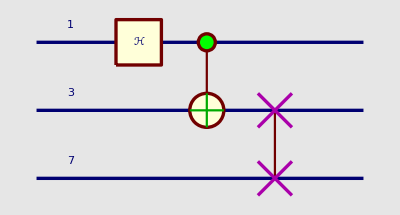

```mathematica
QuantumPlot[Subscript[𝒮𝒲𝒜𝒫, OverHat[7],OverHat[3]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·Subscript[ℋ, OverHat[1]]]
```

Here we specify that qubit OverHat[2] must also be included in the plot. Notice that with this notation the added qubit is plotted at the top of the circuit:

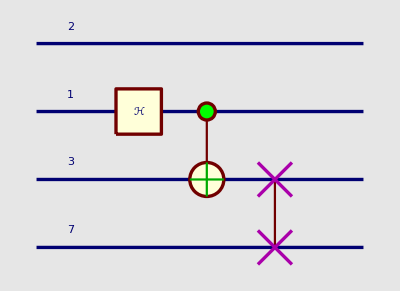

```mathematica
QuantumPlot[Subscript[𝒮𝒲𝒜𝒫, OverHat[7],OverHat[3]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·Subscript[ℋ, OverHat[1]],QubitList->{OverHat[2]}]
```

The option QubitList can also be used to specify in which order the qubits should be plotted. As an example, QubitList→{OverHat[7],OverHat[2]} means that qubit OverHat[7] must be plotted first, then qubit OverHat[2], and the rest of the qubits must be plotted in "canonical order":

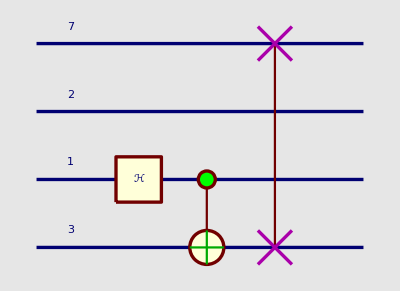

```mathematica
QuantumPlot[Subscript[𝒮𝒲𝒜𝒫, OverHat[7],OverHat[3]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·Subscript[ℋ, OverHat[1]],QubitList->{OverHat[7],OverHat[2]}]
```

If QubitList is set to be a positive integer n, then it is transformed to the list of all the qubits OverHat[1],OverHat[2]...n̂

```mathematica
QubitList->7
```

QubitList→{OverHat[1],OverHat[2],OverHat[3],OverHat[4],OverHat[5],OverHat[6],OverHat[7]}

If QubitList is set to be a positive integer n, then it is transformed to the list of all the qubits OverHat[1],OverHat[2]...n̂

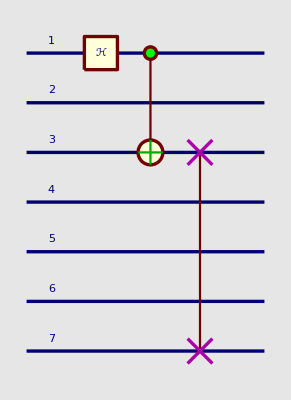

```mathematica
QuantumPlot[Subscript[𝒮𝒲𝒜𝒫, OverHat[7],OverHat[3]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·Subscript[ℋ, OverHat[1]],QubitList->7]
```

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx